```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,10}];
```

```mathematica
SolarModel0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\SolarRotation\\BalbusEquation\\SolarModelBS2005-AGS,OP","Table"];

SolarModel=Drop[SolarModel0,1];
SolarModel=Drop[SolarModel,-3];

RadiusMass=Table[{ Rsun*SolarModel[[All,2]][[i]],Msun*SolarModel[[All,1]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusTemp=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,3]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusDens=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,4]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusPress=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,5]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusLumin=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusFlux=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]/(4*Pi*(RadiusTemp[[i]][[1]])^2)},{i,1,Dimensions[SolarModel][[1]]}];
RadiusGrav=Table[{RadiusMass[[i]][[1]],G*RadiusMass[[i]][[2]]/(RadiusMass[[i]][[1]])^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];

RDown=Rsun*0.03;
RUp=Rsun*0.27;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
```

```mathematica
(* THESE APPLY IN THE RADIATIVE ZONE *)
σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
SoundSpeed[R_,z_]=√(γ P[R,z] / ρ[R,z]);
```

```mathematica
Mu=0.62;   γ=5/3;

kRoss=20; (* Rosseland opacity at 0.7 Rsun*)
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
ξrad[R_,z_] = (γ-1)*χ[R,z];   (*this is what Menou and Balbus call ξrad*)

Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(kRoss*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
Pr[R_,z_]=ν[R,z]/χ[R,z];
```

```mathematica
Plotχ=Plot[χ[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.05,0.25},Frame->True,FrameLabel->{"r/Rsun","χ (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
Show[LogPlot[ν[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.05,0.25},PlotStyle->Directive[Black],PlotRange->{{0.05,0.25},{0.001,100}}],LogPlot[νdyn[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.05,0.25},PlotStyle->Directive[Black,Dashed],PlotRange->{{0.05,0.25},{0.001,100}}],LogPlot[νrad[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.05,0.25},PlotStyle->Directive[Black,Dotted],PlotRange->{{0.05,0.25},{0.001,100}}],Frame->True,FrameLabel->{"r/Rsun","ν (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
PlotPr=Plot[Pr[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.05,0.25},Frame->True,FrameLabel->{"r/Rsun","Pr"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
```

```mathematica
CaptionGeneral[{{"ν", Black, Automatic},{"ν_rad",Black,Dotted}}];
```

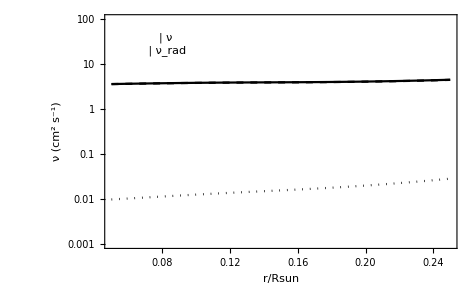
```mathematica
Plotν=-Graphics-;
```